# SQ-8 Helix OD, CD, Pump-Test & TRCD Spektren for 2-State Model

```mathematica
<<ModList.m
<<StylePlot.m
```

## Experiment

```mathematica
SetDirectory["/home/lindorfer/Post-Doc/TRCD/Experiment"];
Data=Import["Abs und CD pSQ-R2s in acetone.txt","Table"];
Data=Drop[Data,3];

ExpCD=Take2[Data,1,2];
ExpOD=Take2[Data,1,3];
```

```mathematica
Ev2nm[Energy_]:=1239.84193 / Energy
```

```mathematica
Ev2nm[2.1423]
```

578.743

```mathematica
Ev2nm[3.4117]
```

363.409

```mathematica
Ev2nm[2.1423]-Ev2nm[3.4117]
```

215.335

## Linear CD & OD Spectra

```mathematica
SetDirectory[NotebookDirectory[]]

OD=Import["CD_OD_Dis.out","Table"];
OD=Take2[OD,1,3];

CD=Import["CD_OD_Dis.out","Table"];
CD=Take2[CD,1,2];
```

/home/lindorfer/Post-Doc/TRCD/Spectra

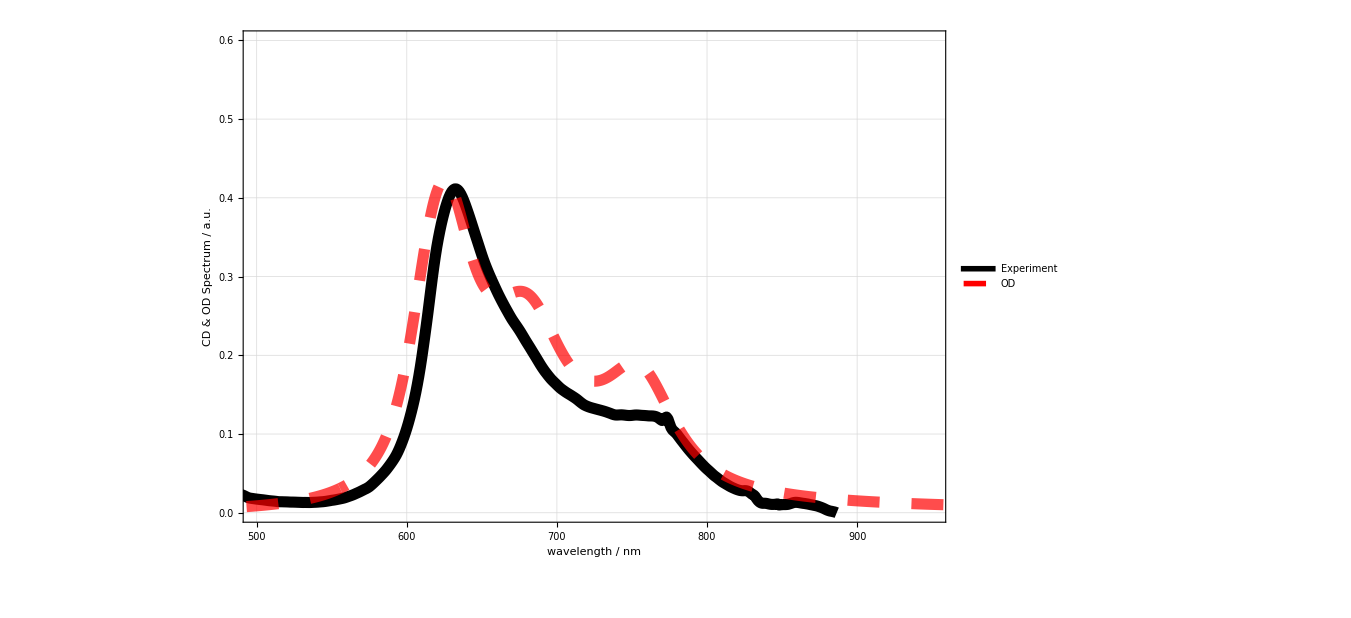

```mathematica
PlotLinSpecOD=StyleListPlot[{ExpOD,ShiftX[ScaleY[OD,3],0]},

PlotStyle->{{Black,Thickness[0.008]},{Red,Opacity[0.7],Dashing[0.023],Thickness[0.008]},{Blue,Opacity[0.7],Dashing[{0.001,0.01}],Thickness[0.008]},{Green,Opacity[0.7],Dashing[{0.001,0.01}],Thickness[0.008]}},
PlotRange->{{500,950},{0,0.6}},
FrameLabels->{{"CD & OD Spectrum / a.u.",""},{"wavelength / nm",""}},
LegendText->Map[Style[#,{Bold,FontFamily->"Helvetica"}]&,{"Experiment","OD"}],
LegendPlacement->{{0.15,0.25}},
PlotLegendsLineColor->{Directive[Black,AbsoluteThickness[5]],Directive[Red,AbsoluteThickness[5],Dashing[0.028]],Directive[Blue,AbsoluteThickness[5]],Directive[Green,AbsoluteThickness[5],Dashing[0.028]]},
GridLinesStyle->Directive[Gray, Dashed],
LegendSpacing->{0.1,-1.2},
ImageSize->1000
]
```

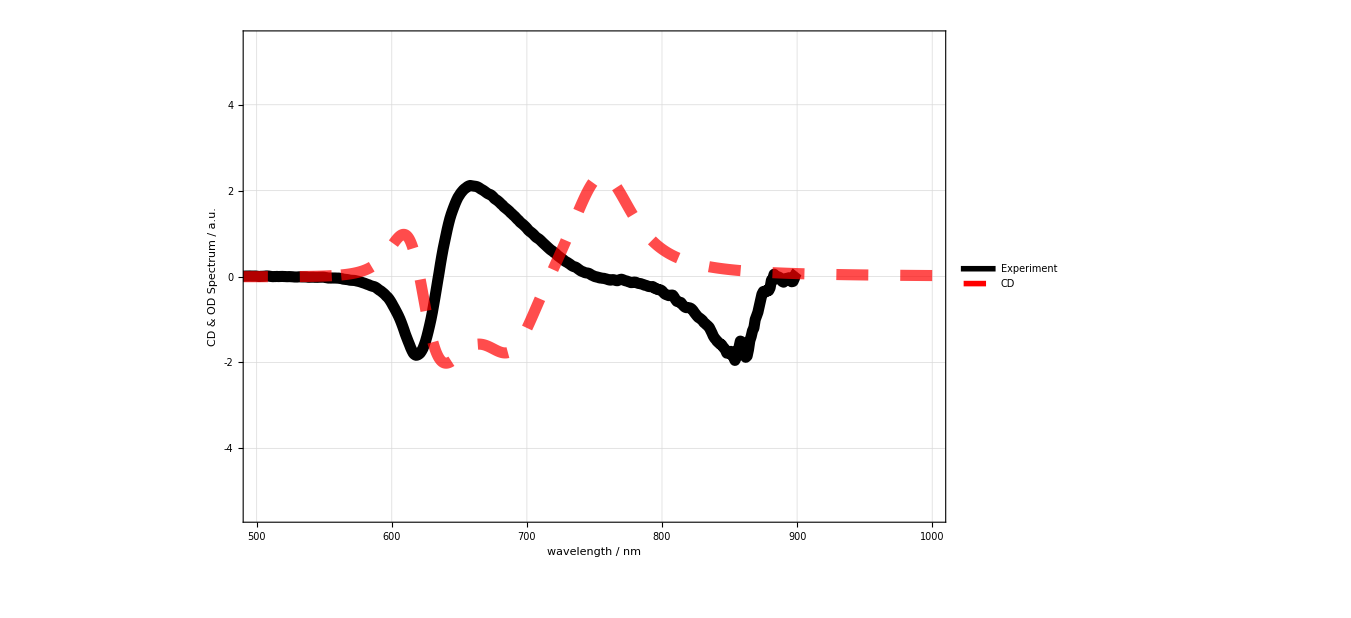

```mathematica
PlotLinSpecCD=StyleListPlot[{ExpCD,ShiftX[ScaleY[CD,2],0]},

PlotStyle->{{Black,Thickness[0.008]},{Red,Opacity[0.7],Dashing[0.023],Thickness[0.008]},{Blue,Opacity[0.7],Dashing[{0.001,0.01}],Thickness[0.008]},{Green,Opacity[0.7],Dashing[{0.001,0.01}],Thickness[0.008]}},
PlotRange->{{500,1000},{-5.5,5.5}},
FrameLabels->{{"CD & OD Spectrum / a.u.",""},{"wavelength / nm",""}},
LegendText->Map[Style[#,{Bold,FontFamily->"Helvetica"}]&,{"Experiment","CD"}],
LegendPlacement->{{0.15,0.25}},
PlotLegendsLineColor->{Directive[Black,AbsoluteThickness[5]],Directive[Red,AbsoluteThickness[5],Dashing[0.028]],Directive[Blue,AbsoluteThickness[5]],Directive[Green,AbsoluteThickness[5],Dashing[0.028]]},
GridLinesStyle->Directive[Gray, Dashed],
LegendSpacing->{0.1,-1.2},
ImageSize->1000
]
```

# Export

```mathematica
SetDirectory[NotebookDirectory[]]
Export["CD_2State.pdf",-Graphics-]
Export["OD_2State.pdf",-Graphics-]
```

/home/lindorfer/Post-Doc/TRCD/Spectra

CD_2State.pdf

OD_2State.pdf